```mathematica
Seq = 100;
Jonhat=3.0167;
joff=3.4817;
goff=5.91;
koff=3.9019;
Gon= Seq 3.0167/(1.+joff/goff);
Jon=(3.0167 Seq-Gon);
Kon=(Seq koff/(1.+(kb Seq/ku)*Jonhat/(joff+goff))-Gon+Seq goff*Jonhat/(joff+goff));
α = 1.5;
ku=1.9799;kb=6.6155 /Seq;
rstar=(Jon+Gon)/(joff+goff);sstar=(Kon+Gon-goff*rstar)/(koff);
cstar=(kb/ku)*rstar*sstar;
```

```mathematica
CoefficientArrays[{0==Gon+Jon-goff (dr[t])-joff (dr[t])-α (kb (dr[t]sstar+rstar ds[t])+ξb)-ξg+ξG-ξj+ξJ+α ((dc[t]) ku+ξu),0==+dc[t] ku+Kon-goff dr[t]-koff ds[t]-kb (dr[t]sstar+rstar ds[t])-ξb-ξg+ξG-ξk+ξK+ξu,
0==-(dc[t] ku)+kb (dr[t]sstar+ ds[t]rstar)+ξb-ξu},{dr[t],ds[t],dc[t]}]
```

{SparseArray[…],SparseArray[…]}

```mathematica
A = -SparseArray[…];
```

```mathematica
MatrixForm[A]
```

(-goff-joff-kb sstar α | -kb rstar α | ku α
-goff-kb sstar | -koff-kb rstar | ku
kb sstar | kb rstar | -ku)

```mathematica
B = -SparseArray[…]
```

SparseArray[…]

```mathematica
e = Eigenvalues[A]
```

{-17.7533,-3.12279,-1.30871}

```mathematica
V = Eigenvectors[A]
```

{{0.748267,0.6204,-0.234949},{0.359774,-0.799205,0.481491},{0.235738,-0.0473932,0.97066}}

```mathematica
Solve[{B[[1]]==a V[[1,1]] + b V[[2,1]] + c V[[3,1]],B[[2]]==a V[[1,2]] + b V[[2,2]] + c V[[3,2]],B[[3]]==a V[[1,3]] + b V[[2,3]] + c V[[3,3]]},{a,b,c}]
```

Solve::ivar: -1.33352 (0.752938 (-3.0167+1.5 ξb+ξg-1. ξG+ξj-1. ξJ-1.5 ξu)+0.188403 (1. ξb-ξu)+0.235713 (-3.78035+ξb+ξg-1. ξG+ξk-1. ξK-1. ξu)+0.0170508 (-1. ξb+ξu)) is not a valid variable.

Solve[{-3.0167+1.5 ξb+ξg-1. ξG+ξj-1. ξJ-1.5 ξu==0.479767 (0.591062 (-3.0167+1.5 ξb+ξg-1. ξG+ξj-1. ξJ-1.5 ξu)-0.781699 (-3.78035+ξb+ξg-1. ξG+ξk-1. ξK-1. ξu)-0.181714 (-1. ξb+ξu))+0.997831 (0.752938 (-3.0167+1.5 ξb+ξg-1. ξG+ξj-1. ξJ-1.5 ξu)+0.188403 (1. ξb-ξu)+0.235713 (-3.78035+ξb+ξg-1. ξG+ξk-1. ξK-1. ξu)+0.0170508 (-1. ξb+ξu))+0.314362 (-0.110944 (-3.0167+1.5 ξb+ξg-1. ξG+ξj-1. ξJ-1.5 ξu)+0.444812 (-3.78035+ξb+ξg-1. ξG+ξk-1. ξK-1. ξu)+0.821222 (-1. ξb+ξu)),-3.78035+ξb+ξg-1. ξG+ξk-1. ξK-1. ξu==-1.06576 (0.591062 (-3.0167+1.5 ξb+ξg-1. ξG+ξj-1. ξJ-1.5 ξu)-0.781699 (-3.78035+ξb+ξg-1. ξG+ξk-1. ξK-1. ξu)-0.181714 (-1. ξb+ξu))+0.827317 (0.752938 (-3.0167+1.5 ξb+ξg-1. ξG+ξj-1. ξJ-1.5 ξu)+0.188403 (1. ξb-ξu)+0.235713 (-3.78035+ξb+ξg-1. ξG+ξk-1. ξK-1. ξu)+0.0170508 (-1. ξb+ξu))-0.0631999 (-0.110944 (-3.0167+1.5 ξb+ξg-1. ξG+ξj-1. ξJ-1.5 ξu)+0.444812 (-3.78035+ξb+ξg-1. ξG+ξk-1. ξK-1. ξu)+0.821222 (-1. ξb+ξu)),-1. ξb+ξu==0.642079 (0.591062 (-3.0167+1.5 ξb+ξg-1. ξG+ξj-1. ξJ-1.5 ξu)-0.781699 (-3.78035+ξb+ξg-1. ξG+ξk-1. ξK-1. ξu)-0.181714 (-1. ξb+ξu))-0.31331 (0.752938 (-3.0167+1.5 ξb+ξg-1. ξG+ξj-1. ξJ-1.5 ξu)+0.188403 (1. ξb-ξu)+0.235713 (-3.78035+ξb+ξg-1. ξG+ξk-1. ξK-1. ξu)+0.0170508 (-1. ξb+ξu))+1.2944 (-0.110944 (-3.0167+1.5 ξb+ξg-1. ξG+ξj-1. ξJ-1.5 ξu)+0.444812 (-3.78035+ξb+ξg-1. ξG+ξk-1. ξK-1. ξu)+0.821222 (-1. ξb+ξu))},{-1.33352 (0.752938 (-3.0167+1.5 ξb+ξg-1. ξG+ξj-1. ξJ-1.5 ξu)+0.188403 (1. ξb-ξu)+0.235713 (-3.78035+ξb+ξg-1. ξG+ξk-1. ξK-1. ξu)+0.0170508 (-1. ξb+ξu)),-1.33352 (0.591062 (-3.0167+1.5 ξb+ξg-1. ξG+ξj-1. ξJ-1.5 ξu)-0.781699 (-3.78035+ξb+ξg-1. ξG+ξk-1. ξK-1. ξu)-0.181714 (-1. ξb+ξu)),1.33352 (-0.110944 (-3.0167+1.5 ξb+ξg-1. ξG+ξj-1. ξJ-1.5 ξu)+0.444812 (-3.78035+ξb+ξg-1. ξG+ξk-1. ξK-1. ξu)+0.821222 (-1. ξb+ξu))}]

```mathematica
{a,b,c}={-((-B⟦3⟧ V⟦2,2⟧ V⟦3,1⟧+B⟦2⟧ V⟦2,3⟧ V⟦3,1⟧+B⟦3⟧ V⟦2,1⟧ V⟦3,2⟧-B⟦1⟧ V⟦2,3⟧ V⟦3,2⟧-B⟦2⟧ V⟦2,1⟧ V⟦3,3⟧+B⟦1⟧ V⟦2,2⟧ V⟦3,3⟧)/(V⟦1,3⟧ V⟦2,2⟧ V⟦3,1⟧-V⟦1,2⟧ V⟦2,3⟧ V⟦3,1⟧-V⟦1,3⟧ V⟦2,1⟧ V⟦3,2⟧+V⟦1,1⟧ V⟦2,3⟧ V⟦3,2⟧+V⟦1,2⟧ V⟦2,1⟧ V⟦3,3⟧-V⟦1,1⟧ V⟦2,2⟧ V⟦3,3⟧)),-((B⟦3⟧ V⟦1,2⟧ V⟦3,1⟧-B⟦2⟧ V⟦1,3⟧ V⟦3,1⟧-B⟦3⟧ V⟦1,1⟧ V⟦3,2⟧+B⟦1⟧ V⟦1,3⟧ V⟦3,2⟧+B⟦2⟧ V⟦1,1⟧ V⟦3,3⟧-B⟦1⟧ V⟦1,2⟧ V⟦3,3⟧)/(V⟦1,3⟧ V⟦2,2⟧ V⟦3,1⟧-V⟦1,2⟧ V⟦2,3⟧ V⟦3,1⟧-V⟦1,3⟧ V⟦2,1⟧ V⟦3,2⟧+V⟦1,1⟧ V⟦2,3⟧ V⟦3,2⟧+V⟦1,2⟧ V⟦2,1⟧ V⟦3,3⟧-V⟦1,1⟧ V⟦2,2⟧ V⟦3,3⟧)),-((B⟦3⟧ V⟦1,2⟧ V⟦2,1⟧-B⟦2⟧ V⟦1,3⟧ V⟦2,1⟧-B⟦3⟧ V⟦1,1⟧ V⟦2,2⟧+B⟦1⟧ V⟦1,3⟧ V⟦2,2⟧+B⟦2⟧ V⟦1,1⟧ V⟦2,3⟧-B⟦1⟧ V⟦1,2⟧ V⟦2,3⟧)/(-V⟦1,3⟧ V⟦2,2⟧ V⟦3,1⟧+V⟦1,2⟧ V⟦2,3⟧ V⟦3,1⟧+V⟦1,3⟧ V⟦2,1⟧ V⟦3,2⟧-V⟦1,1⟧ V⟦2,3⟧ V⟦3,2⟧-V⟦1,2⟧ V⟦2,1⟧ V⟦3,3⟧+V⟦1,1⟧ V⟦2,2⟧ V⟦3,3⟧))}
```

{-1.33352 (-0.0170508 (ξb-ξu)-0.188403 (-ξb+ξu)-0.235713 (3.78035-ξb-ξg+1. ξG-ξk+1. ξK+1. ξu)-0.752938 (3.0167-1.5 ξb-ξg+1. ξG-ξj+1. ξJ+1.5 ξu)),-1.33352 (0.181714 (ξb-ξu)+0.781699 (3.78035-ξb-ξg+1. ξG-ξk+1. ξK+1. ξu)-0.591062 (3.0167-1.5 ξb-ξg+1. ξG-ξj+1. ξJ+1.5 ξu)),1.33352 (0.821222 (ξb-ξu)+0.444812 (3.78035-ξb-ξg+1. ξG-ξk+1. ξK+1. ξu)-0.110944 (3.0167-1.5 ξb-ξg+1. ξG-ξj+1. ξJ+1.5 ξu))}

```mathematica
Diff = ReplaceAll[{{Select[Expand[a^2],MemberQ[#,ξb^2|ξu^2|ξK^2|ξk^2|ξj^2|ξJ^2|ξg^2 |ξG^2]|| FreeQ[#,ξb|ξu|ξK|ξk|ξj|ξJ|ξg |ξG]&] ,Select[Expand[a b],MemberQ[#,ξb^2|ξu^2|ξK^2|ξk^2|ξj^2|ξJ^2|ξg^2 |ξG^2]|| FreeQ[#,ξb|ξu|ξK|ξk|ξj|ξJ|ξg |ξG]&] ,Select[Expand[a c],MemberQ[#,ξb^2|ξu^2|ξK^2|ξk^2|ξj^2|ξJ^2|ξg^2 |ξG^2]|| FreeQ[#,ξb|ξu|ξK|ξk|ξj|ξJ|ξg |ξG]&]},{Select[Expand[b a],MemberQ[#,ξb^2|ξu^2|ξK^2|ξk^2|ξj^2|ξJ^2|ξg^2 |ξG^2]|| FreeQ[#,ξb|ξu|ξK|ξk|ξj|ξJ|ξg |ξG]&], Select[Expand[b^2],MemberQ[#,ξb^2|ξu^2|ξK^2|ξk^2|ξj^2|ξJ^2|ξg^2 |ξG^2]|| FreeQ[#,ξb|ξu|ξK|ξk|ξj|ξJ|ξg |ξG]&] ,Select[Expand[b c],MemberQ[#,ξb^2|ξu^2|ξK^2|ξk^2|ξj^2|ξJ^2|ξg^2 |ξG^2]|| FreeQ[#,ξb|ξu|ξK|ξk|ξj|ξJ|ξg |ξG]&]} ,
{Select[Expand[c a],MemberQ[#,ξb^2|ξu^2|ξK^2|ξk^2|ξj^2|ξJ^2|ξg^2 |ξG^2]|| FreeQ[#,ξb|ξu|ξK|ξk|ξj|ξJ|ξg |ξG]&] ,
Select[Expand[c b],MemberQ[#,ξb^2|ξu^2|ξK^2|ξk^2|ξj^2|ξJ^2|ξg^2 |ξG^2]|| FreeQ[#,ξb|ξu|ξK|ξk|ξj|ξJ|ξg |ξG]&] ,
Select[Expand[c^2],MemberQ[#,ξb^2|ξu^2|ξK^2|ξk^2|ξj^2|ξJ^2|ξg^2 |ξG^2]|| FreeQ[#,ξb|ξu|ξK|ξk|ξj|ξJ|ξg |ξG]&] }},{ξJ^2 -> Jon,ξK^2 -> Kon,ξG^2 -> Gon,ξj^2 -> joff rstar,ξk^2 -> koff sstar,ξg^2 -> goff rstar,ξb^2 ->2 kb rstar sstar, ξu^2 ->2 ku cstar}]
```

{{2661.48,240.887,-340.669},{240.887,634.831,-418.025},{-340.669,-418.025,430.638}}

```mathematica
AutoCorr[t_] ={Sum[Sum[(V[[k,1]]V[[l,1]])/(e[[k]]+e[[l]])Diff[[k,l]](Exp[e[[k]](Abs[t]-t)/2+e[[l]](Abs[t]+t)/2]),{l,1,3}],{k,1,3}] / Sum[Sum[(V[[k,1]]V[[l,1]])/(e[[k]]+e[[l]])Diff[[k,l]],{l,1,3}],{k,1,3}],Sum[Sum[(V[[k,2]]V[[l,2]])/(e[[k]]+e[[l]])Diff[[k,l]](Exp[e[[k]](Abs[t]-t)/2+e[[l]](Abs[t]+t)/2]),{l,1,3}],{k,1,3}] / Sum[Sum[(V[[k,2]]V[[l,2]])/(e[[k]]+e[[l]])Diff[[k,l]],{l,1,3}],{k,1,3}],Sum[Sum[(V[[k,3]]V[[l,3]])/(e[[k]]+e[[l]])Diff[[k,l]](Exp[e[[k]](Abs[t]-t)/2+e[[l]](Abs[t]+t)/2]),{l,1,3}],{k,1,3}] / Sum[Sum[(V[[k,3]]V[[l,3]])/(e[[k]]+e[[l]])Diff[[k,l]],{l,1,3}],{k,1,3}]}
```

{-0.0207573 (-41.969 ⅇ^(-8.87663 (-t+Abs[t])-8.87663 (t+Abs[t]))-3.10636 ⅇ^(-1.56139 (-t+Abs[t])-8.87663 (t+Abs[t]))+3.15247 ⅇ^(-0.654355 (-t+Abs[t])-8.87663 (t+Abs[t]))-3.10636 ⅇ^(-8.87663 (-t+Abs[t])-1.56139 (t+Abs[t]))-13.1566 ⅇ^(-1.56139 (-t+Abs[t])-1.56139 (t+Abs[t]))+8.00039 ⅇ^(-0.654355 (-t+Abs[t])-1.56139 (t+Abs[t]))+3.15247 ⅇ^(-8.87663 (-t+Abs[t])-0.654355 (t+Abs[t]))+8.00039 ⅇ^(-1.56139 (-t+Abs[t])-0.654355 (t+Abs[t]))-9.1432 ⅇ^(-0.654355 (-t+Abs[t])-0.654355 (t+Abs[t]))),-0.0130537 (-28.8509 ⅇ^(-8.87663 (-t+Abs[t])-8.87663 (t+Abs[t]))+5.72131 ⅇ^(-1.56139 (-t+Abs[t])-8.87663 (t+Abs[t]))-0.525475 ⅇ^(-0.654355 (-t+Abs[t])-8.87663 (t+Abs[t]))+5.72131 ⅇ^(-8.87663 (-t+Abs[t])-1.56139 (t+Abs[t]))-64.9235 ⅇ^(-1.56139 (-t+Abs[t])-1.56139 (t+Abs[t]))+3.57294 ⅇ^(-0.654355 (-t+Abs[t])-1.56139 (t+Abs[t]))-0.525475 ⅇ^(-8.87663 (-t+Abs[t])-0.654355 (t+Abs[t]))+3.57294 ⅇ^(-1.56139 (-t+Abs[t])-0.654355 (t+Abs[t]))-0.369548 ⅇ^(-0.654355 (-t+Abs[t])-0.654355 (t+Abs[t]))),-0.00999152 (-4.13775 ⅇ^(-8.87663 (-t+Abs[t])-8.87663 (t+Abs[t]))+1.30535 ⅇ^(-1.56139 (-t+Abs[t])-8.87663 (t+Abs[t]))-4.07574 ⅇ^(-0.654355 (-t+Abs[t])-8.87663 (t+Abs[t]))+1.30535 ⅇ^(-8.87663 (-t+Abs[t])-1.56139 (t+Abs[t]))-23.5647 ⅇ^(-1.56139 (-t+Abs[t])-1.56139 (t+Abs[t]))+44.0867 ⅇ^(-0.654355 (-t+Abs[t])-1.56139 (t+Abs[t]))-4.07574 ⅇ^(-8.87663 (-t+Abs[t])-0.654355 (t+Abs[t]))+44.0867 ⅇ^(-1.56139 (-t+Abs[t])-0.654355 (t+Abs[t]))-155.015 ⅇ^(-0.654355 (-t+Abs[t])-0.654355 (t+Abs[t])))}

```mathematica
CrossCorr[t_] ={-Sum[Sum[(V[[k,1]]V[[l,2]])/(e[[k]]+e[[l]])Diff[[k,l]](Exp[e[[k]](Abs[t]-t)/2+e[[l]](Abs[t]+t)/2]),{l,1,3}],{k,1,3}] / Sqrt[Sum[Sum[(V[[k,1]]V[[l,1]])/(e[[k]]+e[[l]])Diff[[k,l]],{l,1,3}],{k,1,3}] Sum[Sum[(V[[k,2]]V[[l,2]])/(e[[k]]+e[[l]])Diff[[k,l]],{l,1,3}],{k,1,3}]],-Sum[Sum[(V[[k,3]]V[[l,2]])/(e[[k]]+e[[l]])Diff[[k,l]](Exp[e[[k]](Abs[t]-t)/2+e[[l]](Abs[t]+t)/2]),{l,1,3}],{k,1,3}] / Sqrt[Sum[Sum[(V[[k,3]]V[[l,3]])/(e[[k]]+e[[l]])Diff[[k,l]],{l,1,3}],{k,1,3}] Sum[Sum[(V[[k,2]]V[[l,2]])/(e[[k]]+e[[l]])Diff[[k,l]],{l,1,3}],{k,1,3}]],-Sum[Sum[(V[[k,1]]V[[l,3]])/(e[[k]]+e[[l]])Diff[[k,l]](Exp[e[[k]](Abs[t]-t)/2+e[[l]](Abs[t]+t)/2]),{l,1,3}],{k,1,3}] / Sqrt[Sum[Sum[(V[[k,1]]V[[l,1]])/(e[[k]]+e[[l]])Diff[[k,l]],{l,1,3}],{k,1,3}] Sum[Sum[(V[[k,3]]V[[l,3]])/(e[[k]]+e[[l]])Diff[[k,l]],{l,1,3}],{k,1,3}]]}
```

{0.0164609 (34.7972 ⅇ^(-8.87663 (-t+Abs[t])-8.87663 (t+Abs[t]))+2.57553 ⅇ^(-1.56139 (-t+Abs[t])-8.87663 (t+Abs[t]))-2.61376 ⅇ^(-0.654355 (-t+Abs[t])-8.87663 (t+Abs[t]))-6.9005 ⅇ^(-8.87663 (-t+Abs[t])-1.56139 (t+Abs[t]))-29.2263 ⅇ^(-1.56139 (-t+Abs[t])-1.56139 (t+Abs[t]))+17.7721 ⅇ^(-0.654355 (-t+Abs[t])-1.56139 (t+Abs[t]))+0.633778 ⅇ^(-8.87663 (-t+Abs[t])-0.654355 (t+Abs[t]))+1.60841 ⅇ^(-1.56139 (-t+Abs[t])-0.654355 (t+Abs[t]))-1.83817 ⅇ^(-0.654355 (-t+Abs[t])-0.654355 (t+Abs[t]))),0.0114205 (-10.926 ⅇ^(-8.87663 (-t+Abs[t])-8.87663 (t+Abs[t]))+3.44687 ⅇ^(-1.56139 (-t+Abs[t])-8.87663 (t+Abs[t]))-10.7623 ⅇ^(-0.654355 (-t+Abs[t])-8.87663 (t+Abs[t]))+2.1667 ⅇ^(-8.87663 (-t+Abs[t])-1.56139 (t+Abs[t]))-39.114 ⅇ^(-1.56139 (-t+Abs[t])-1.56139 (t+Abs[t]))+73.1775 ⅇ^(-0.654355 (-t+Abs[t])-1.56139 (t+Abs[t]))-0.199001 ⅇ^(-8.87663 (-t+Abs[t])-0.654355 (t+Abs[t]))+2.15256 ⅇ^(-1.56139 (-t+Abs[t])-0.654355 (t+Abs[t]))-7.56872 ⅇ^(-0.654355 (-t+Abs[t])-0.654355 (t+Abs[t]))),0.0144013 (-13.1779 ⅇ^(-8.87663 (-t+Abs[t])-8.87663 (t+Abs[t]))-0.97537 ⅇ^(-1.56139 (-t+Abs[t])-8.87663 (t+Abs[t]))+0.989848 ⅇ^(-0.654355 (-t+Abs[t])-8.87663 (t+Abs[t]))+4.15729 ⅇ^(-8.87663 (-t+Abs[t])-1.56139 (t+Abs[t]))+17.6077 ⅇ^(-1.56139 (-t+Abs[t])-1.56139 (t+Abs[t]))-10.707 ⅇ^(-0.654355 (-t+Abs[t])-1.56139 (t+Abs[t]))-12.9804 ⅇ^(-8.87663 (-t+Abs[t])-0.654355 (t+Abs[t]))-32.9419 ⅇ^(-1.56139 (-t+Abs[t])-0.654355 (t+Abs[t]))+37.6475 ⅇ^(-0.654355 (-t+Abs[t])-0.654355 (t+Abs[t])))}

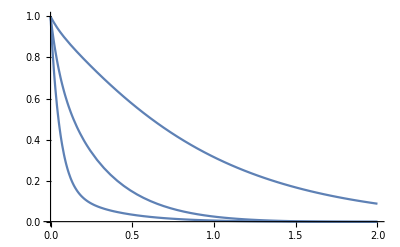

```mathematica
Plot[AutoCorr[[1]][t],{t,0,2},PlotRange->All]
```

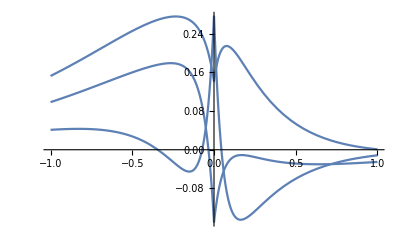

```mathematica
Plot[CrossCorr[[1]][t],{t,-1,1},PlotRange->All]
```